```mathematica
DrawColorfulReinhardtPolygon[rv_]:=Module[{diams, fans,hull, verts,curpt,lastpt,nextpt,sign,j,k,n,angle},
n=Apply[Plus,rv];
lastpt={0,0};
curpt={1,0};  (* Current point in the construction *)
verts={lastpt,curpt};
diams={Line[verts]};
fans={};
hull={};
sign=1;          (* Sign of current term *)
angle=0;
For[k=1,k≤Length[rv],k++,
sign = -sign;
For[j=1,j<rv[[k]],j++,
angle+=Pi/n;
nextpt=curpt +  sign N[{Cos[angle], Sin[-angle]},12];
AppendTo[fans,Line[{curpt,nextpt}]];
AppendTo[verts, nextpt];
AppendTo[hull,Line[{lastpt,nextpt}]];
lastpt=nextpt;
];
angle+=Pi/n;
nextpt=curpt +  sign N[{Cos[angle], Sin[-angle]},12];
AppendTo[diams,Line[{curpt,nextpt}]];
AppendTo[verts, nextpt];
AppendTo[hull,Line[{lastpt,nextpt}]];
(*lastpt=nextpt;*)
lastpt=curpt;
curpt=nextpt;
];
(*Print["hull: ", hull];Print["diams: ",diams];Print["verts: ",verts];*)
Show[Graphics[Join[{Thickness[.004], Red},fans,{Thickness[.007],Blue},Take[diams,Length[diams]-1],{Thickness[.007],Black},hull]]]
(*Show[Graphics[Join[hull,diams]],AspectRatio->Automatic]*)
];
dcrp=DrawColorfulReinhardtPolygon;
```

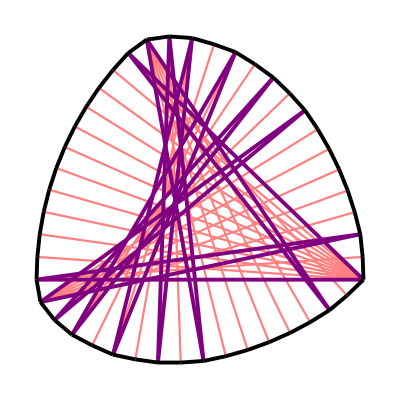

```mathematica
dcrp[{11 ,2 ,1 ,6 ,1 ,2 ,1 ,2 ,2 ,2 ,2 ,1 ,2 ,1 ,6 ,1, 2
}]
```

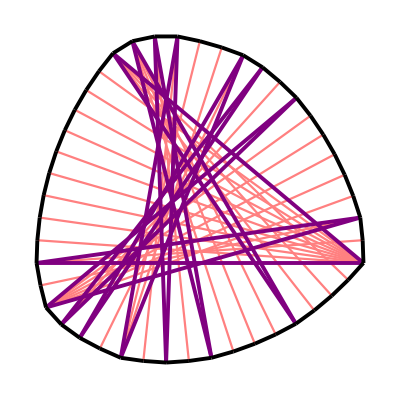

```mathematica
dcrp[{10, 4, 1 ,4 ,1 ,2 ,1 ,2 ,3 ,2 ,1 ,1 ,2 ,1 ,6 ,2, 2}]
```

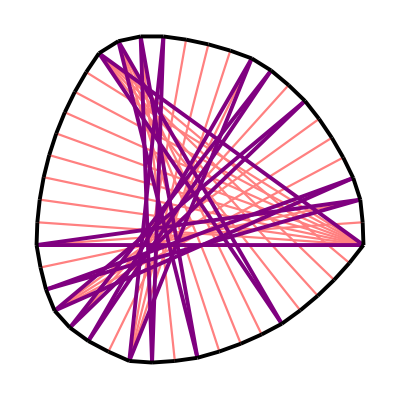

```mathematica
dcrp[{9 ,5 ,1 ,4 ,1 ,2 ,1 ,1 ,4 ,2 ,1 ,1 ,2 ,1 ,4 ,1 ,1 ,2 ,2
}]
```

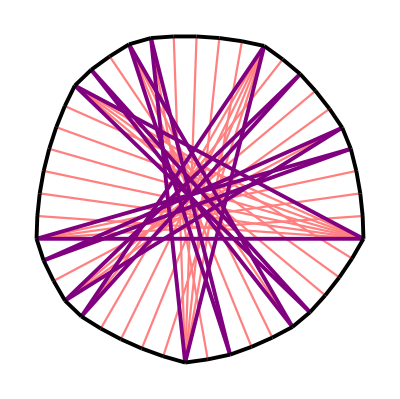

```mathematica
dcrp[{7 ,4 ,1 ,1 ,2 ,3 ,1 ,2 ,5 ,5 ,2 ,1 ,3 ,2 ,1 ,1 ,4}]
```

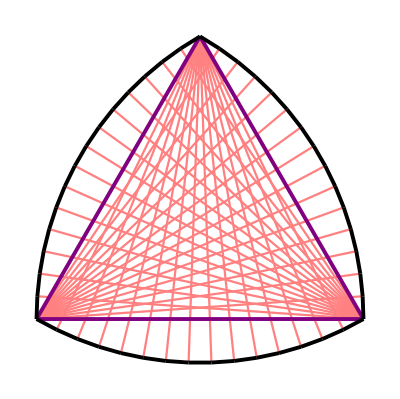

```mathematica
dcrp[{15,15,15}]
```

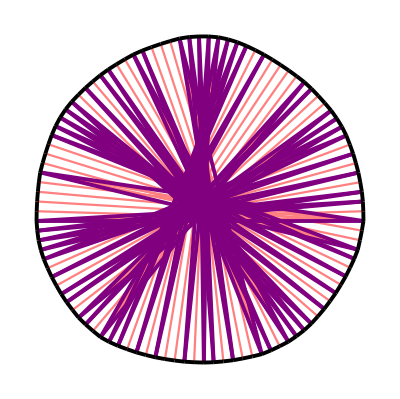

```mathematica
dcrp[{5, 3 ,4 ,1 ,1, 2, 1 ,2 ,1 ,2 ,1 ,2 ,2 ,1 ,2 ,1 ,1 ,1 ,3 ,2 ,1 ,1 ,4 ,3 ,1 ,2 ,1 ,1 ,1 ,2 ,1, 3, 1, 2, 1, 2, 1, 1, 2, 1, 5, 2, 1, 1, 3, 2, 1, 1, 1, 2, 1, 2, 2, 1, 2, 1 ,2 ,1 ,1 ,1 ,2 }]
```

```mathematica
dcrp[{5, 3 ,4 ,1 ,1 ,2 ,1 ,2 ,1 ,2 ,1 ,2 ,2 ,1 ,2 ,1 ,1 ,1 ,3 ,2 ,1 ,1 ,4 ,3 ,1 ,2 ,1 ,1 ,1 ,2 ,1 ,3 ,1 ,2 ,1 ,2 ,1 ,1 ,2 ,1 ,5 ,2 ,1 ,1 ,3 ,2 ,1 ,1 ,1 ,2 ,1 ,2 ,2 ,1 ,2 ,1 ,2 ,1 ,1 ,1 ,2}]
```

```mathematica
dcrp[{5 ,3, 3, 2 ,2 ,2 ,1 ,1 ,3 ,2 ,1 ,1 ,3 ,2 ,1 ,1 ,1 ,2 ,1, 3, 1, 1, 2, 2, 2, 2, 2, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 2, 1, 1, 1, 1, 2, 1 ,3 ,3 ,3 ,3 ,2 ,1 ,1 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,3 ,2 ,1 ,1 ,2}]
```

```mathematica
Total[{6 ,1 ,3 ,2 ,1 ,1 ,1 ,2 ,1 ,2 ,2 ,1 ,1 ,1 ,2 ,2 ,1, 1, 1, 2, 1, 5, 1, 4, 1, 1, 2, 1, 2, 1, 2, 1, 2, 1 ,1 ,2 ,2 ,1 ,1 ,1 ,1 ,2 ,1 ,1, 3 ,2 ,3 ,1 ,2 ,1 ,1 ,1 ,2 ,1 ,3 ,1 ,1 ,1 ,2 ,2 ,1 ,4, 1}]
```

105

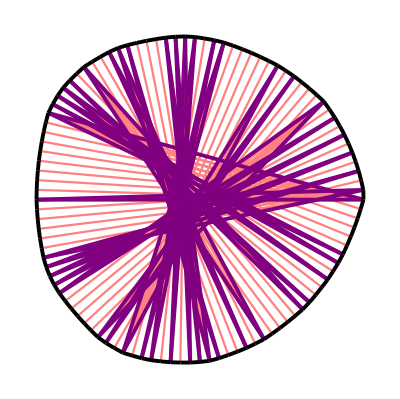

```mathematica
dcrp[{9 ,6 ,1 ,1 ,1 ,2 ,1 ,3 ,1 ,1 ,2 ,5 ,3, 2, 1, 3, 1, 1, 4, 1, 1, 1, 1, 2, 1, 2, 2, 1, 1, 2, 6, 2, 2, 1, 4, 6, 2, 1, 2, 1, 2, 1, 2, 1, 2, 6, 1}]
```

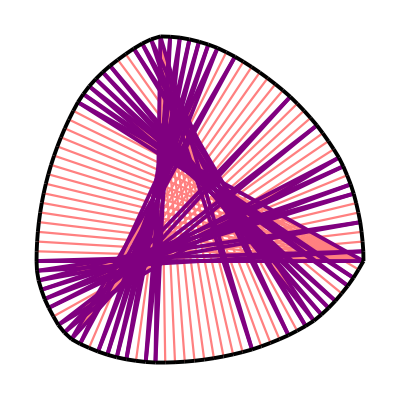

```mathematica
dcrp[{17 ,2 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,1 ,1, 1, 3, 1, 1, 2, 1, 4 ,1, 10 ,1 ,1 ,1 ,2, 1, 1, 1, 1 ,1, 1, 1, 2, 2, 1, 7, 1, 4 ,1 ,4 ,2 ,1 ,1 ,2 ,1 ,1 ,1 ,3 ,1 ,3 ,1, 1}]
```

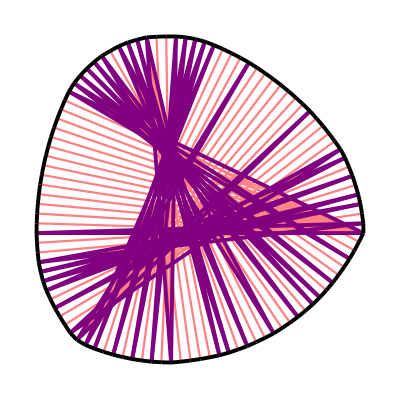

```mathematica
dcrp[{15, 3, 1, 3, 1, 2, 1, 1, 1, 2, 1, 3, 2, 3, 1, 2, 1, 1, 1, 5, 3, 2, 1, 2, 1, 2, 1, 2, 1, 1, 4, 1, 8, 1, 5, 3, 1, 2, 2, 1, 2, 1, 1, 1, 2, 3, 1}]
```

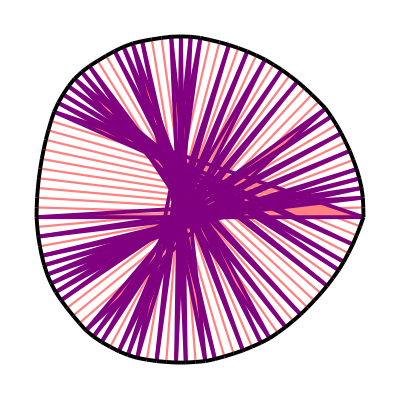

```mathematica
dcrp[{11, 3, 1, 2, 1, 1, 1, 2, 1, 4, 1, 2, 1, 2, 3, 1, 1, 2, 1 ,3 ,1 ,1 ,3 ,2 ,1 ,1 ,1 ,2 ,1 ,2 ,3 ,1 ,2 ,1 ,2 ,2 ,2, 1, 2, 1, 4, 4, 1, 1, 2, 1, 2, 1, 2, 1, 1, 1 ,1, 2, 1, 2, 2}]
```

```mathematica
Total[{5, 2, 3, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 2, 1, 3, 2, 1, 2, 4, 1, 3, 1, 2, 1, 1, 1, 1, 1, 1, 2, 1, 1, 1, 3, 2, 4 ,4 ,4 ,1 ,3 ,2 ,3 ,1 ,1 ,3 ,2 ,1 ,1 ,3 ,2 ,3 ,2 ,1 ,2 ,2 ,1}]
```

105

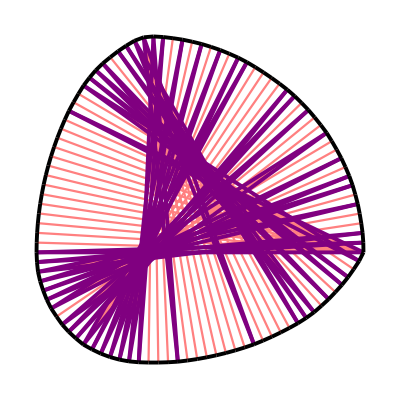

```mathematica
dcrp[{15 ,1 ,3, 2 ,1 ,1 ,1 ,2 ,1 ,2 ,2 ,1 ,1 ,1 ,1 ,5 ,1 ,8 ,1 ,4 ,1 ,1 ,2 ,1 ,2 ,1 ,2 ,1 ,2 ,1 ,1 ,1 ,5 ,1 ,1 ,1 ,2 ,1 ,3 ,2 ,3 ,1 ,2 ,1, 1, 1, 2, 1, 3, 1, 1, 1, 1}]
```

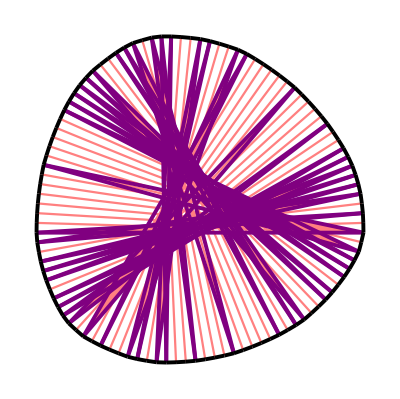

```mathematica
dcrp[{7, 2 ,6 ,1, 1 ,1 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,3 ,3 ,1 ,1 ,2 ,1 ,5 ,2 ,4 ,1 ,3 ,1 ,1 ,3 ,2 ,1 ,1 ,3 ,3 ,1 ,2 ,6 ,2 ,5 ,1 ,3 ,1 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,1 ,1 ,2 ,2 ,1 ,2}]
```

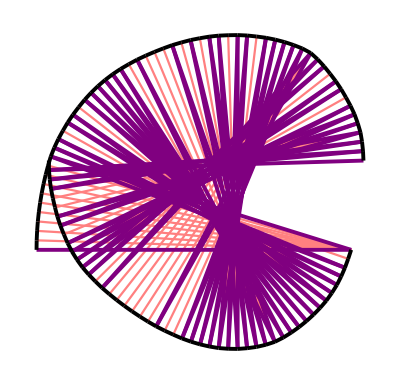

```mathematica
dcrp[{10 ,2 ,1 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,2 ,1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 2, 1, 4, 1, 2, 1, 2, 1, 1, 1, 2, 1, 1, 1, 2, 1, 1, 1, 1, 1, 1, 1 ,1, 3, 1, 7 ,1 ,2 ,1 ,1 ,2 ,1 ,1, 1, 2, 1, 1 ,2 ,1 ,1 ,1 ,3 ,1 ,1 ,1 ,1 ,1 ,1}]
```

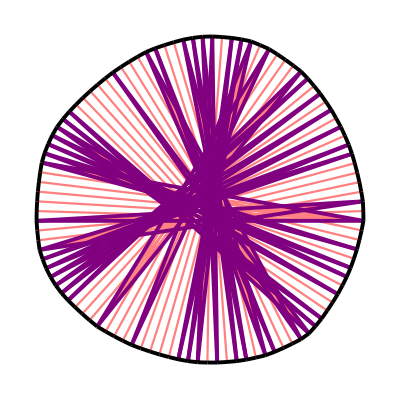

```mathematica
dcrp[{6 ,3 ,1, 2, 1, 1, 1, 2, 1, 3, 1, 1, 1, 1, 6, 1, 4, 3, 1, 1, 3, 2, 1, 1, 1, 2, 1, 2, 2, 1, 1, 1, 1, 5, 2, 4, 4, 4, 1, 1, 2, 1, 2, 1, 2, 1, 2, 1, 1, 1, 5, 3, 2}]
```

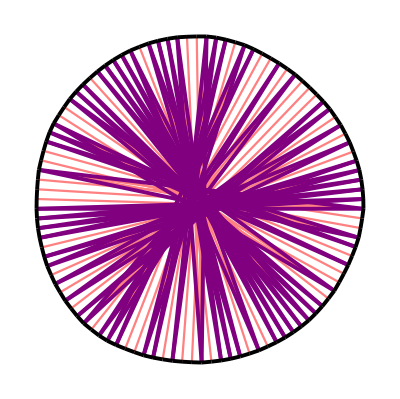

```mathematica
dcrp[{4 ,3 ,3 ,1 ,1 ,2 ,1 ,3 ,3 ,2 ,1 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,1 ,1, 1, 1, 1, 2, 2, 2, 1, 1, 1, 1, 1, 2, 3, 3, 1, 2, 1, 1, 2, 3, 1, 1, 3, 1, 2, 2, 4, 1, 1, 2, 2, 2, 2, 2, 2, 1, 1, 2, 1, 1, 1, 1, 1, 1, 1}]
```

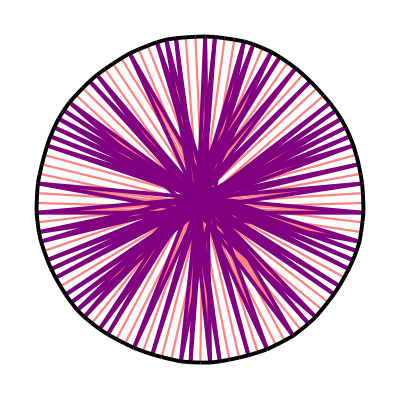

```mathematica
dcrp[{3,3,4,1,1,1,1,1,1,2,1,1,1,3,3,1,1,2,4,3,3,2,1,3,1,1,3,2,1,1,3,3,1,2,2,3,1,1,2,2,2,1,3,1,1,1,1,2,1,1,1,1,1,2,2,1,2,2,3}]
```

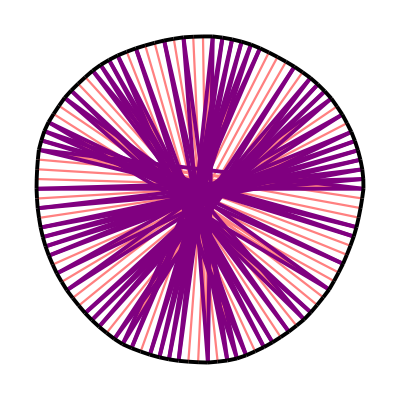

```mathematica
dcrp[{4 ,4 ,1 ,1 ,1 ,3 ,1 ,3 ,3 ,3 ,1 ,1 ,3 ,2 ,1 ,2 ,1 ,1 ,1 ,2 ,2 ,1 ,3 ,1 ,2 ,2 ,3, 3, 1, 1, 1,1 ,1 ,1, 1 ,2, 1, 1, 4,1 ,2 ,2 ,1 ,1 ,1, 1, 1, 3, 2, 2, 2, 2,1 ,1 ,1 ,1 ,1 ,1 ,1 ,2 ,1 ,2,1}]
```

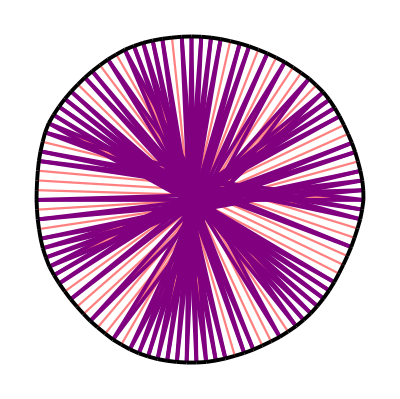

```mathematica
dcrp[{4, 1, 1, 1 ,2 ,3 ,1 ,4 ,1 ,1 ,1 ,1 ,1 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,2 ,2 ,2 ,3 ,1 ,1, 1, 2, 1,1, 1, 1, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 2, 1 ,1 ,1 ,2 ,1 ,2, 2, 3, 3, 2 ,3, 1, 2, 1, 1 ,1 ,1 ,3 ,1 ,1 ,1 ,2 ,1 ,1 ,2 ,1 ,2 ,1}]
```

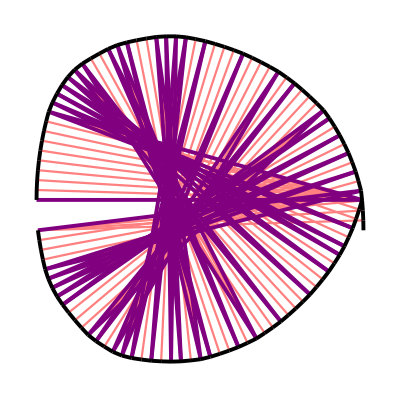

```mathematica
dcrp[{9, 3 ,1 ,2 ,1 ,1 ,1 ,2 ,1 ,3 ,1 ,4 ,1 ,3 ,3 ,2 ,1 ,3 ,1 ,1 ,3 ,2 ,1 ,1 ,1 ,2 ,1 ,2 ,2 ,1 ,4 ,1 ,4 ,2, 2,1, 4, 4, 1, 1, 2, 1, 2, 1, 2, 1, 2, 4, 4}]
```

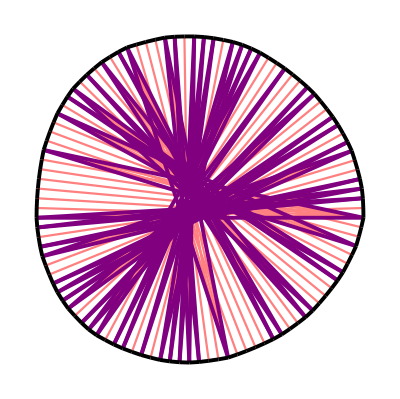

```mathematica
dcrp[{7 ,3 ,4 ,3 ,2 ,1 ,1 ,4 ,2 ,1 ,2 ,3 ,2 ,1 ,1 ,5 ,4 ,3 ,1 ,1 ,2 ,1 ,1 ,1 ,1 ,1 ,2 ,2 ,1 ,2 ,1 ,1 ,1 ,2 ,3 ,1 ,3 ,1 ,1 ,2 ,3 ,1 ,1 ,1 ,2 ,1 ,1 ,3 ,3 ,1 ,1 ,2 ,1 ,1 ,2 }]
```

```mathematica
dcrp[{11, 3, 1 ,2 ,1 ,1 ,1 ,2 ,1 ,4 ,1 ,2 ,1 ,2 ,3 ,1 ,1 ,2 ,1 ,3, 1, 1, 3, 2, 1, 1, 1, 2, 1, 2, 3, 1, 2, 1, 2, 2, 2, 1 ,2 ,1 ,4 ,4, 1, 1, 2, 1, 2, 1, 2, 1, 1, 1, 1, 2, 1, 2, 2}]

(* first F added *)
```

-Graphics-

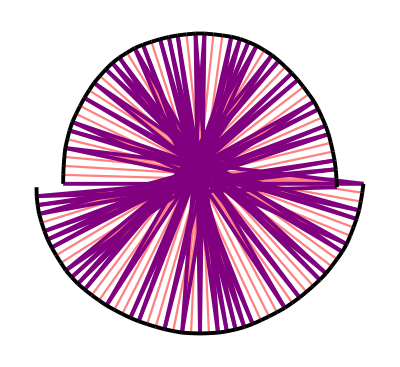

```mathematica
dcrp[{4, 3 ,2 ,1 ,1 ,3 ,3 ,1 ,2 ,3 ,2 ,1 ,1 ,3 ,1 ,2 ,2 ,4 ,1 ,1 ,2 ,1 ,1 ,1 ,1 ,1 ,2 ,2 ,1 ,2 ,3 ,2 ,1 ,3 ,1 ,1 ,1 ,3 ,2 ,3 ,1 ,1 ,2 ,1 ,1 ,1 ,3 ,3, 1, 1, 2, 1, 1 ,2 ,3 ,1 ,1 ,1 ,2 ,1}]
```

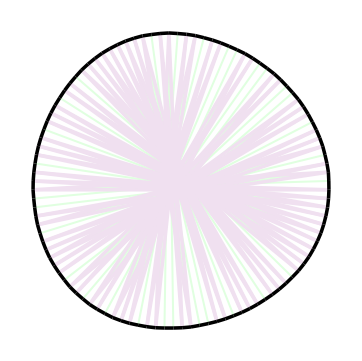

```mathematica
dcrp[{1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,3,2,1,1,3,2,1,1,2,2,1,1,1,3,2,1,1,3,2,1,1,3,2,1,1,1,1,2,1,1,1,1,2,2,1,1,3,2}]
```

```mathematica
(* second F added *)
```

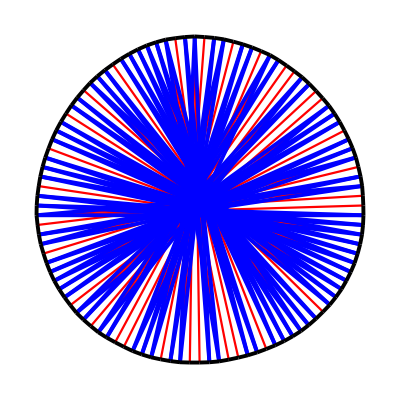

```mathematica
dcrp[{1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,3,2,1,1,3,2,1,1,2,2,1,1,1,2,3,1,1,3,2,1,1,3,2,1,1,1,1,2,1,1,1,1,2,2,1,1,2,3}]
```

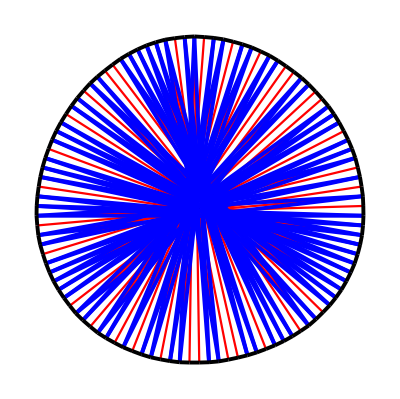

```mathematica
(* third F added *)
dcrp[{1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,2,1,1,3,2,1,1,1,1,1,2,1,1,1,3,2,1,1,3,2,1,1,2,2,1,1,2,2,2,1,1,3,2,1,1,3,2,1,1,1,1,2,1,1,1,1,2,2,1,2,2,2}]
```

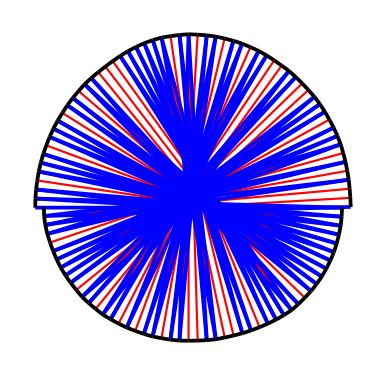

```mathematica
(* sum of -(first) + second + third *)
(* they all share the same f2 and f3, with different g1's *)
dcrp[{1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,2,1,1,4,1,1,1,1,1,1,2,1,1,1,3,2,1,1,3,2,1,1,2,2,1,1,2,2,2,1,1,3,2,1,1,3,2,1,1,1,1,2,1,1,1,1,2,2,1,2,1,3}]
```

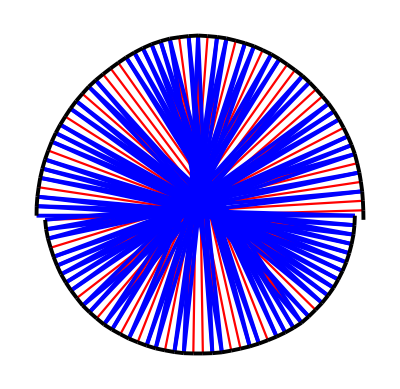

```mathematica
dcrp[{1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,2,1,1,4,1,1,1,1,1,1,2,1,1,1,3,2,1,1,3,2,1,1,2,2,1,1,2,2,2,1,1,3,2,1,1,3,2,1,1,1,1,2,1,1,1,1,2,2,1,2,1,3}]
```

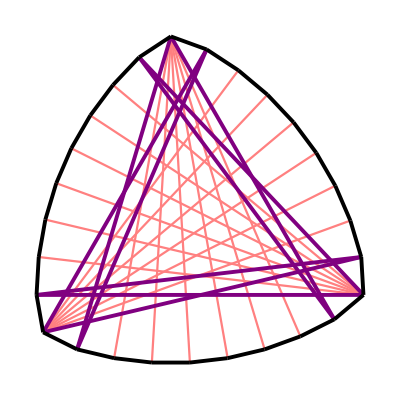

```mathematica
dcrp[{7, 1, 1, 7, 1, 1,7, 1, 1}]
```

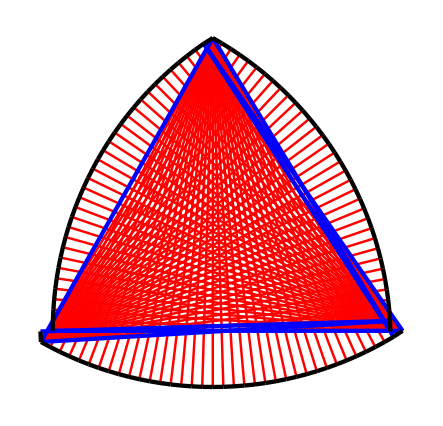

```mathematica
dcrp[{32,1,1,35,33,1,1}]
```

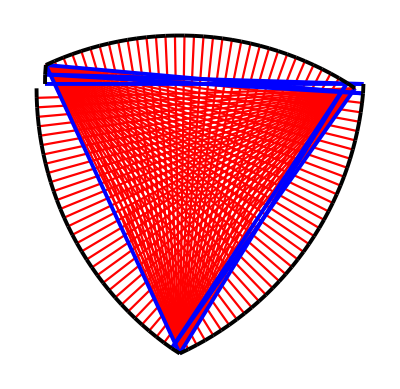

```mathematica
dcrp[{1, 1,1,35,33,1,1,32}]
```

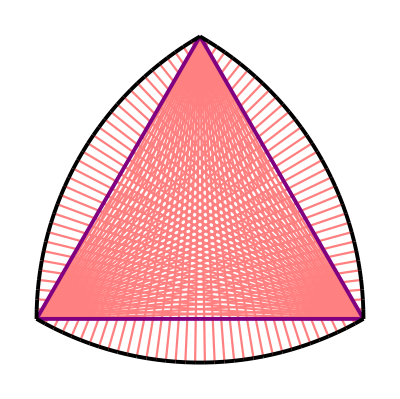

```mathematica
dcrp[{35,35,35}]
```

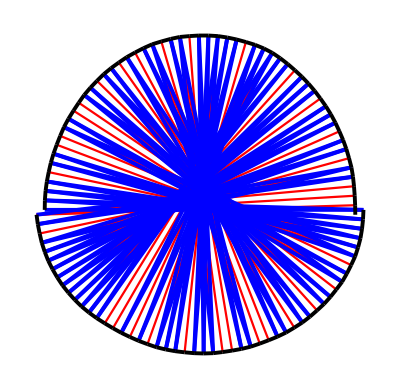

```mathematica
dcrp[{1,1,1,1,1,1,2,1,1,1,3,2,1,1,3,2,1,1,2,2,1,1,2,2,2,1,1,3,2,1,1,3,2,1,1,1,1,2,1,1,1,1,2,2,1,2,1,3,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,2,1,1,4}]
```

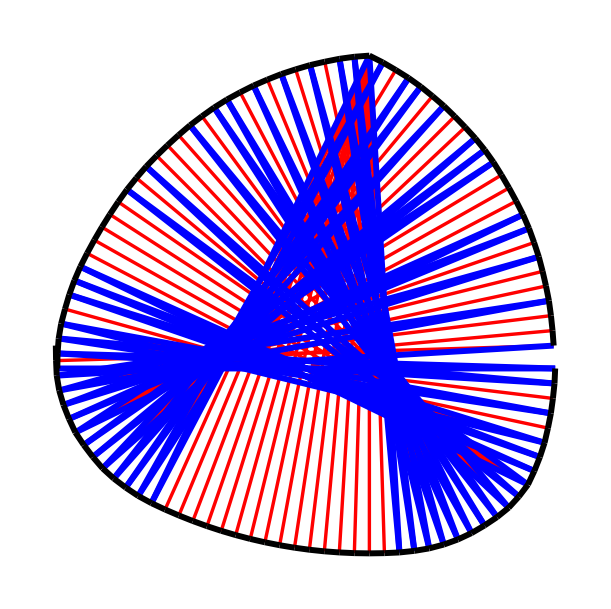

```mathematica
dcrp[{1,1,1,2,1,2,2,1,1,1,1,1,6,1,2,1,4,1,2,1,1,1,2,1,2,1,2,1,2,1,1,1,1,17, 1,1,2,1,1,1,2,1,3,1,1,1,1,1,4,1,1,1,2,1,3,1,3,2}]
```

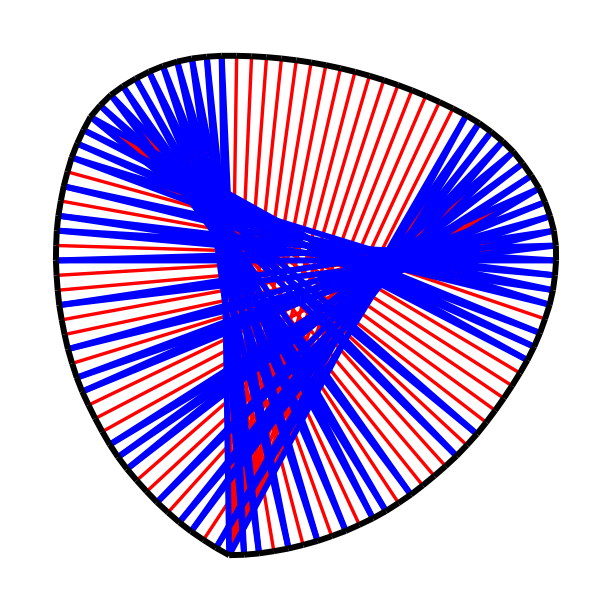

```mathematica
dcrp[{2, 1,1,1,2,1,2,2,1,1,1,1,1,6,1,2,1,4,1,2,1,1,1,2,1,2,1,2,1,2,1,1,1,1,17,1,1,2,1,1,1,2,1,3,1,1,1,1,1,4,1,1,1,2,1,3,1,3,1}]
```

```mathematica
Total[{2,1,1,1,2,1,2,2,1,1,1,1,1,6,1,2,1,4,1,2,1,1,1,2,1,2,1,2,1,2,1,1,1,1,17,1,1,2,1,1,1,2,1,3,1,1,1,1,1,4,1,1,1,2,1,3,1,3}]
```

104

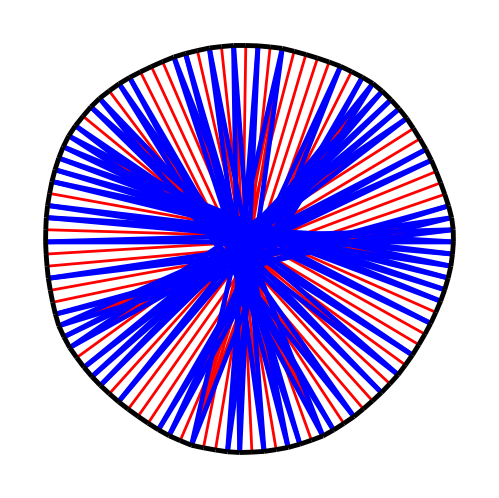

```mathematica
dcrp[{2,1,1,1,2,1,1,1,1,1,1,2,1,3,1,2,2,2,1,3,2,2,1,1,4,2,1,1,2,2,2,2,2,1,2,3,5,2,2,1,1,4,1,2,1,1,1,1,1,2,3,1,1,1,4,1,1,3,1,3,1}]
```

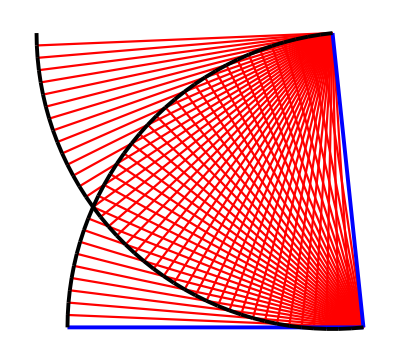

```mathematica
dcrp[{35,40}]
```

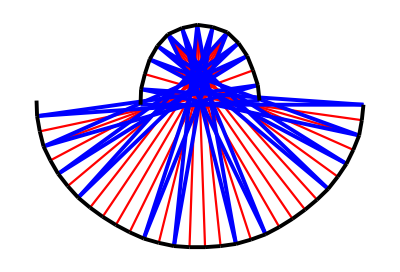

```mathematica
dcrp[{1,2,2,2,1,2,1,5,1,2,1,4,1,2,1,5,1,2,1,2,2,2,1,1}]
```

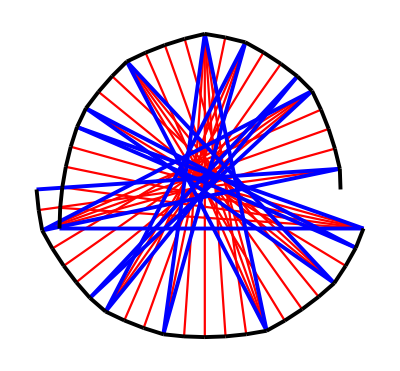

```mathematica
dcrp[{5,1,1,2,3,4,4,5,2,3,3,1,1,4,4,2,1}]
```

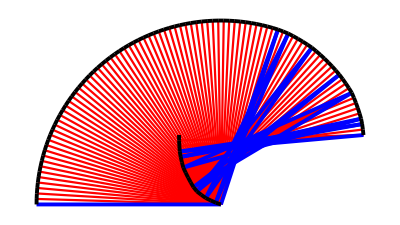

```mathematica
dcrp[{63,1,2,2,5,2,7,1,4,4,5,2,1,1,2,3}]
```

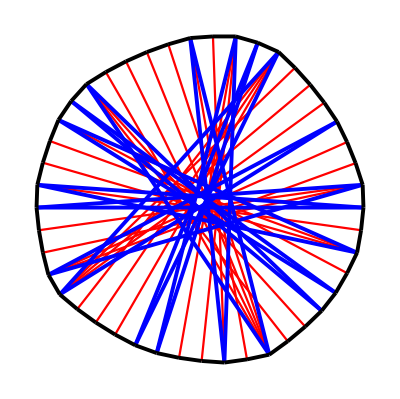

```mathematica
dcrp[{1,2,3,2,1,1,1,3,5,2,2,3,1,1,1,4,4,1,3,3,1}]
```

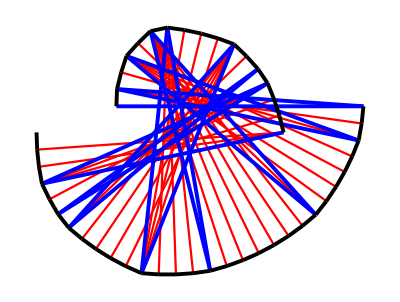

```mathematica
dcrp[{1,2,2,5,2,7,1,4,4,5,2,1,1,2,3,3}]
```

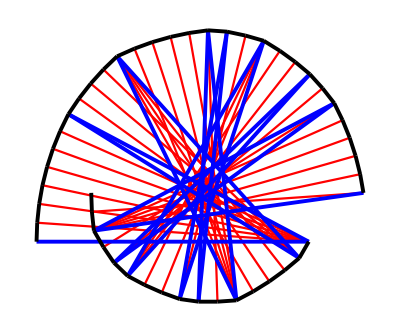

```mathematica
dcrp[{7,1,4,4,5,2,1,1,2,3,3,1,2,2,5,2}]
```

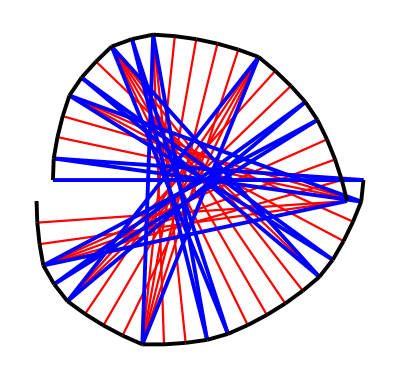

```mathematica
dcrp[{1,1,3,3,1,1,2,5,1,1,1,3,5,4,3,1,1,1,4,3}]
```

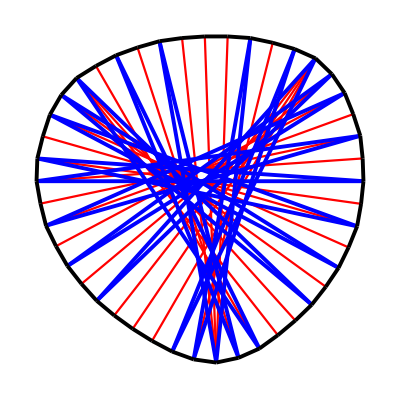

```mathematica
dcrp[{1,2,2,2,1,2,1,3,2,1 ,2 ,1 ,4 ,1 ,2 ,1, 1 ,4 ,1 ,2 ,1 ,2 ,2 ,2 ,2}]
```

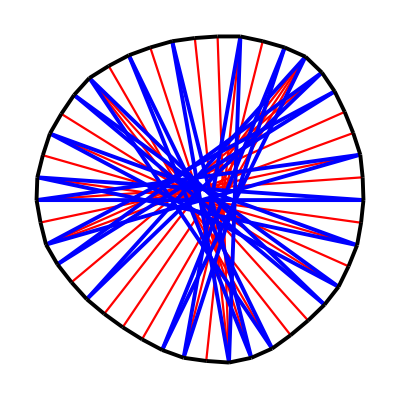

```mathematica
dcrp[{1 ,2 ,2 ,2 ,2 ,1 ,1 ,3 ,2 ,1 ,2 ,1 ,3 ,2 ,2 ,1 ,1 ,4 ,1 ,2 ,1 ,1 ,3 ,2 ,2}]
```

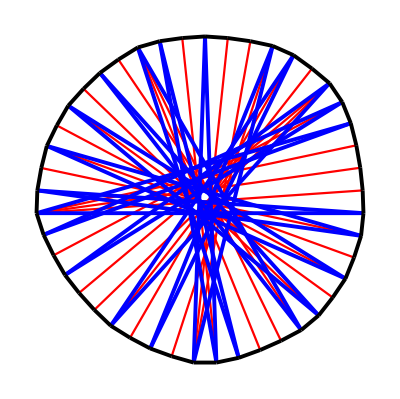

```mathematica
dcrp[{1 ,1 ,2 ,2 ,2 ,2 ,2 ,1 ,2 ,3 ,1 ,1 ,2 ,1 ,3 ,2 ,1 ,2 ,2 ,3 ,1 ,2 ,1 ,1 ,4}]
```

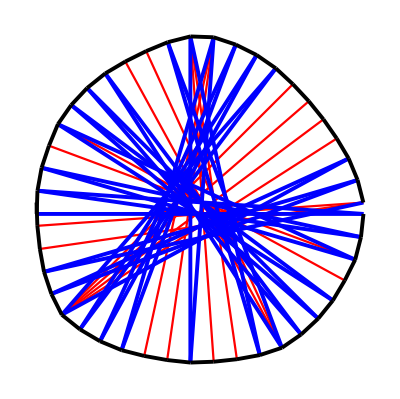

```mathematica
dcrp[{1, 1, 1, 1 ,2 ,2 ,1 ,1 ,1 ,1 ,1 ,1 ,3 ,1 ,1 ,3 ,1 ,3 ,1 ,1 ,1 ,1 ,1 ,1 ,5 ,1 ,1 ,1 ,1 ,3}]
```

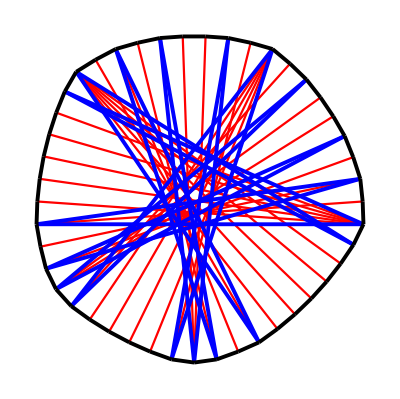

```mathematica
dcrp[{6, 1 ,1 ,6 ,2 ,2 ,2 ,1 ,3 ,1 ,2 ,5 ,2 ,1 ,3 ,1 ,2 ,2 ,2}]
```

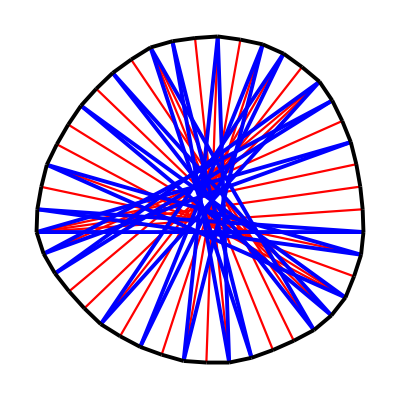

```mathematica
dcrp[{1 ,1 ,2, 2, 3, 1, 2, 1, 2, 3, 1, 1 ,2, 2, 2, 2, 1, 2, 2, 3, 1, 1, 2, 1, 4}]
```

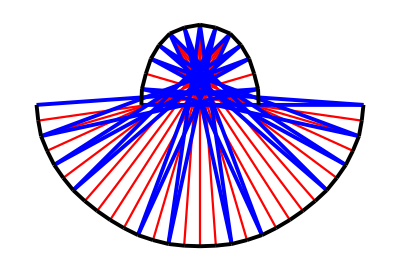

```mathematica
dcrp[{1 ,2 ,2 ,2 ,1 ,2 ,1 ,5 ,1 ,2 ,1 ,4 ,1 ,2 ,1 ,5 ,1 ,2 ,1 ,2 ,2, 2, 1}]
```

```mathematica
Total[{3 ,3 ,1, 1, 1, 2, 4 ,1 ,1 ,1 ,3 ,3 ,1 ,5 ,3 ,1 ,1 ,1 ,3 ,2 ,2 ,1 ,1}]
```

45

```mathematica
Total[{3, 3, 1, 4 ,4 ,1 ,1 ,1 ,3 ,2 ,2 ,5 ,3, 1, 1 ,1 ,2 ,3 ,2 ,1}]
```

44

```mathematica
Total[{3, 3, 1, 4, 4, 1, 1, 1 ,3 ,2 ,2 ,5 ,3 ,1 ,1 ,1 ,2 ,3 ,2 ,1 ,1}]
```

45

```mathematica
Total[{3 ,2 ,2 ,1 ,1 ,3 ,2 ,1, 1, 1 ,1 ,2 ,4 ,1 ,1 ,1 ,2 ,1 ,3 ,1 ,5 ,3 ,1 ,2}]
```

45

```mathematica
Total[{3 ,2 ,2 ,1 ,1 ,2 ,4 ,1 ,1 ,1 ,2 ,4 ,1 ,5 ,3 ,1 ,5 ,2 ,2 ,1}]
```

44

```mathematica
Total[{3 ,2 ,2 ,4, 4 ,1 ,1 ,1 ,2 ,3 ,2 ,5 ,3 ,1 ,4 ,3 ,2 ,1}]
```

44

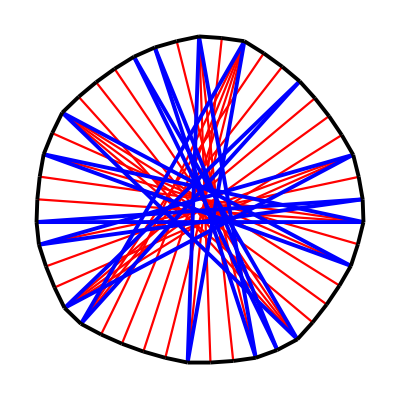

```mathematica
dcrp[{3 ,2 ,2 ,4, 4 ,1 ,1 ,1 ,2 ,3 ,2 ,5 ,3 ,1 ,4 ,3 ,2 ,1,1}]
```

```mathematica
Total[{2, 4 ,1 ,4 ,4 ,1 ,5 ,2 ,2 ,5 ,2 ,2 ,1 ,1 ,2 ,3 ,2 ,1}]
```

44

```mathematica
Total[{2, 3, 2, 4, 4, 1, 4, 3, 2, 5, 2, 2, 4, 3, 2, 1, 1}]
```

45

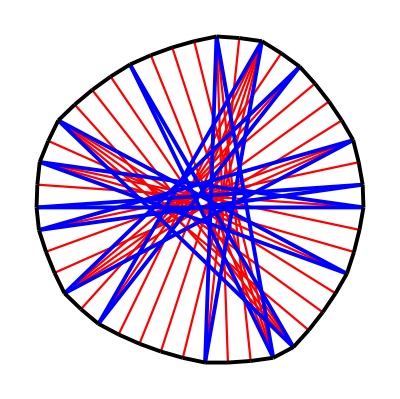

```mathematica
dcrp[{2, 3, 2, 4, 4, 1, 4, 3, 2, 5, 2, 2, 4, 3, 2, 1, 1}]
```

```mathematica
Total[{3 ,4 ,2 ,2 ,5 ,2 ,3 ,4 ,1 ,4 ,4 ,2 ,3 ,2 ,1 ,1 ,2}]
```

45

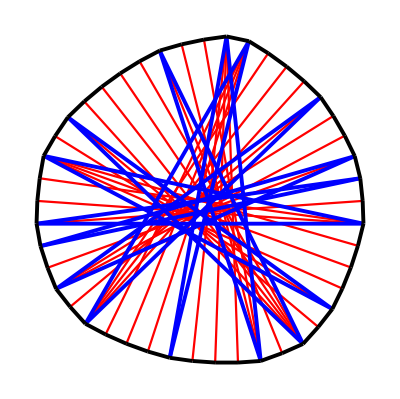

```mathematica
dcrp[{3, 4, 2, 2, 5, 2, 3, 4, 1, 4, 4, 2, 3, 2, 1, 1, 2}]
```

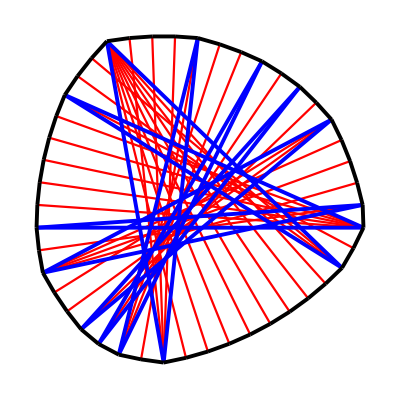

```mathematica
dcrp[{6,2 ,3 ,9 ,4 ,2 ,3 ,1 ,2 ,1 ,2 ,3 ,4, 2,1}]
```

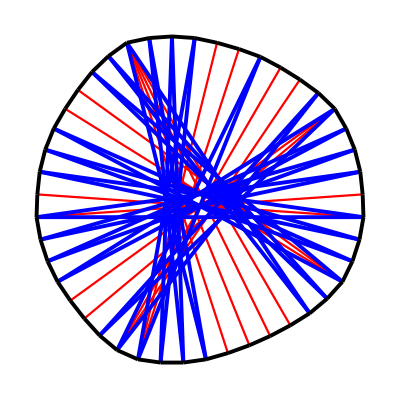

```mathematica
dcrp[{2, 1, 1, 1, 1, 1 ,3 ,1 ,1 ,1 ,1 ,5 ,1 ,1 ,1 ,1 ,1 ,1, 3,1,3,1,1, 3,1,1,1, 1 ,1 ,1 ,2}]
```

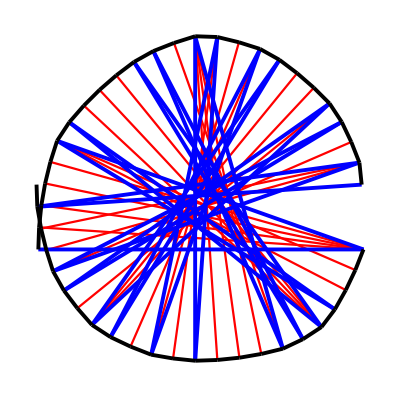

```mathematica
dcrp[{5 ,3, 1, 1, 4, 1 ,1 ,1 ,2 ,4 ,1 ,2 ,2 ,2 ,1 ,1 ,3 ,2 ,1 ,1 ,2 ,3 ,1,1}]
```

```mathematica
Total[{5 ,3, 1, 1, 4, 1 ,1 ,1 ,2 ,4 ,1 ,2 ,2 ,2 ,1 ,1 ,3 ,2 ,1 ,1 ,2 ,3 ,1}]
```

45

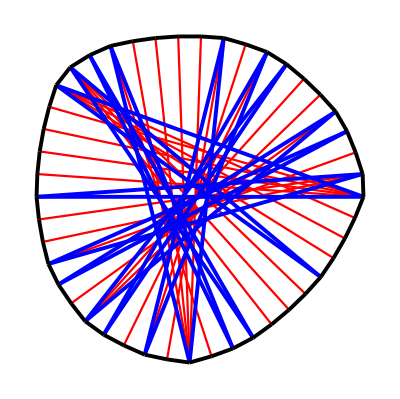

```mathematica
dcrp[{5, 4, 1, 4, 1, 1, 1, 2, 5 ,2 ,2 ,2 ,1 ,1 ,3 ,2 ,1 ,1 ,2 ,3 ,1}]
```

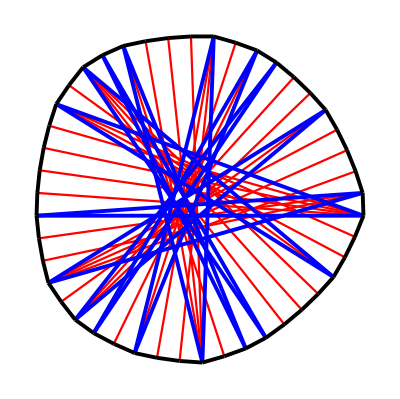

```mathematica
dcrp[{5 ,3 ,2 ,4 ,1 ,1 ,1 ,2 ,4 ,3 ,2 ,2 ,1 ,1 ,3 ,2 ,4 ,3,1}]
```

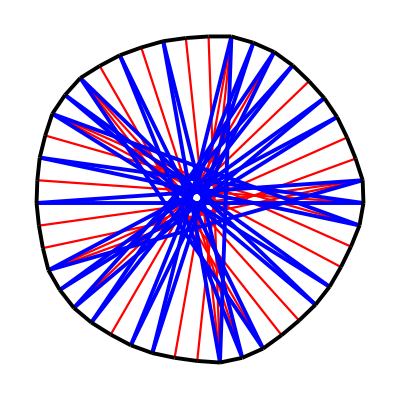

```mathematica
dcrp[{2, 1, 2 ,3 ,1 ,1 ,1 ,3 ,2 ,1 ,2 ,1 ,3 ,3 ,1 ,1 ,1 ,2 ,1 ,1 ,2 ,1 ,1 ,1 ,3 ,3 ,1}]
```

```mathematica
dcrp[{1, 2, 2, 2, 2, 1 ,1 ,3 ,2 ,1 ,2 ,1 ,3 ,2 ,2 ,1 ,1 ,4 ,1 ,2 ,1 ,1 ,3 ,2 ,2}]
```

-Graphics-

```mathematica
dcrp[{6, 2 ,3 ,9 ,4 ,2 ,3 ,1 ,2 ,1 ,2 ,3 ,4 ,2 ,1}]
```

-Graphics-

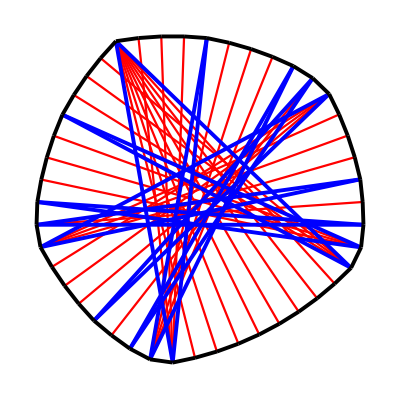

```mathematica
dcrp[{1,1,4,1,4,9,4,1,4,1,1,2,1,4,4,1,2}]
```

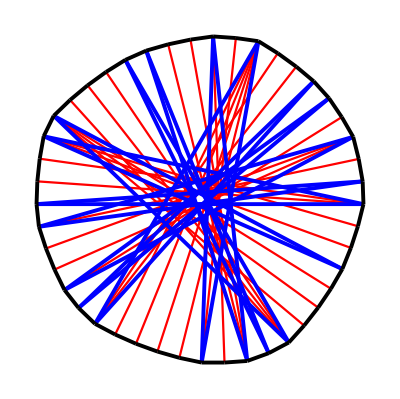

```mathematica
dcrp[{3, 3, 1 ,4 ,4 ,1 ,1 ,1 ,3 ,2 ,2, 5, 3, 1, 1, 1, 2, 3, 2 ,1 ,1}]
```

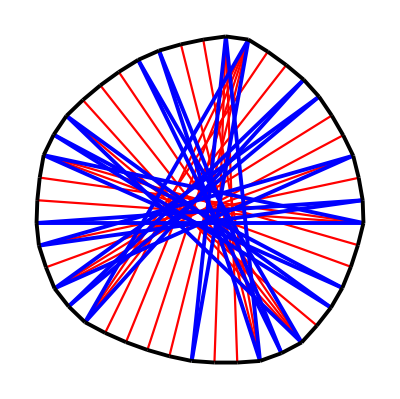

```mathematica
dcrp[{3, 3 ,1 ,1 ,1 ,2 ,4 ,1 ,1 ,1 ,3 ,3 ,1 ,5 ,3 ,1 ,1 ,1 ,3 ,2 ,2 ,1 ,1}]
```

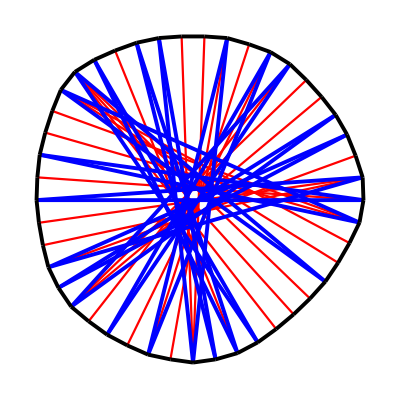

```mathematica
dcrp[{2, 1 ,3 ,3 ,1 ,4 ,1 ,1 ,2 ,1 ,1 ,1 ,3 ,2 ,2 ,2 ,1 ,2 ,3 ,1 ,1 ,1 ,2 ,3 ,1}]
```

```mathematica
dcrp[{5 ,3 ,2 ,4 ,1 ,1 ,1 ,2 ,4 ,3 ,2 ,2 ,1 ,1 ,3 ,2, 4 ,3 ,1}]
```

-Graphics-

```mathematica
dcrp[{2, 3, 2, 4, 4, 1, 4, 3, 2, 5, 2, 2, 4, 3, 2, 1, 1}]
```

-Graphics-

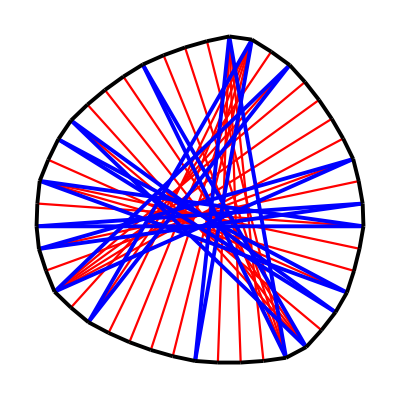

```mathematica
dcrp[{2, 3 ,2 ,1 ,1 ,2 ,4 ,1 ,4 ,4 ,1 ,5 ,2 ,2 ,5 ,2 ,2 ,1 ,1}]
```

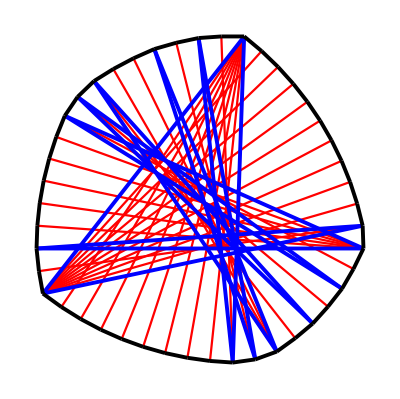

```mathematica
dcrp[{6 ,2 ,1 ,2 ,1 ,2 ,3 ,1 ,2 ,1 ,2 ,9 ,10, 2, 1}]
```

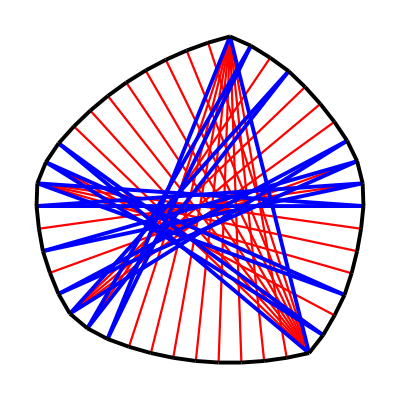

```mathematica
dcrp[{1, 4 ,1 ,2 ,1 ,1 ,9 ,9 ,1 ,1 ,2 ,1 ,4 ,1 ,1 ,2 ,1 ,2 ,1}]
```

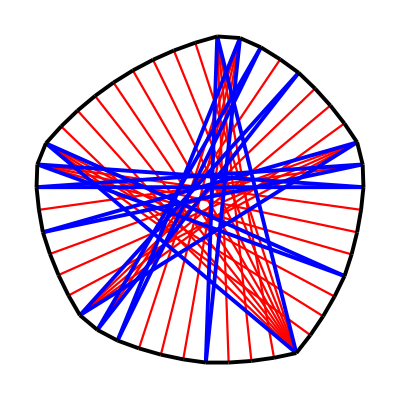

```mathematica
dcrp[{1 ,4 ,1 ,4 ,9 ,4 ,1 ,4 ,1 ,1 ,2 ,1 ,4 ,4 ,1 ,2 ,1}]
```

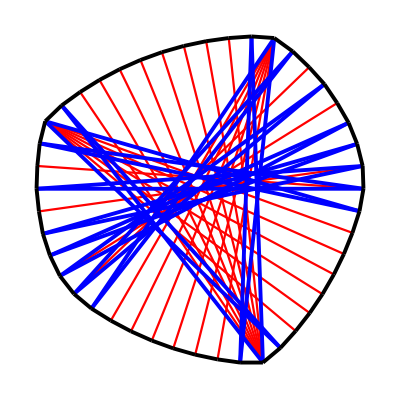

```mathematica
dcrp[{2 ,1 ,1 ,7 ,1 ,1 ,9 ,1 ,1 ,7 ,1 ,1 ,2 ,1 ,2 ,1 ,1 ,1 ,1 ,2 ,1}]
```

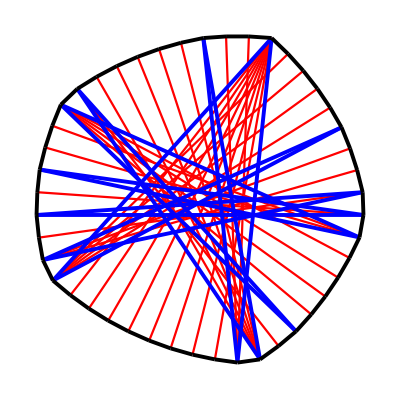

```mathematica
dcrp[{2, 1, 3, 5, 1, 2, 6 ,1 ,3 ,9 ,5 ,1 ,3 ,2 ,1}]
```

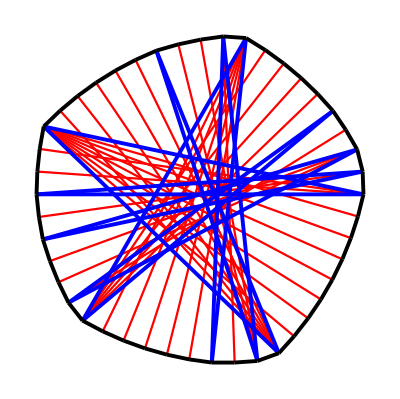

```mathematica
dcrp[{3 ,8 ,6 ,1 ,3 ,2 ,1 ,6 ,5 ,1 ,2 ,3 ,1 ,2 ,1}]
```

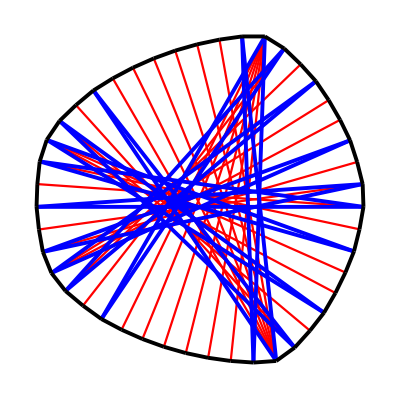

```mathematica
dcrp[{2 ,2 ,1 ,3 ,1 ,2 ,2 ,1 ,7 ,1 ,1 ,7 ,1, 2 ,2 ,1 ,3 ,1 ,2 ,2, 1}]
```

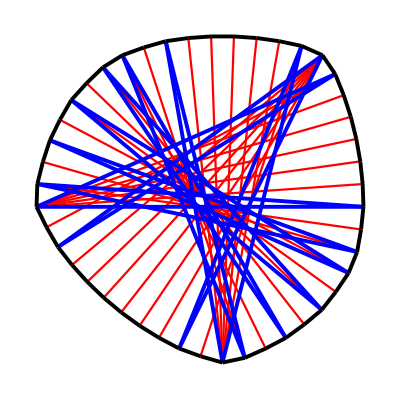

```mathematica
dcrp[{1 ,2 ,2 ,1 ,2 ,2 ,2 ,2 ,1 ,2 ,2, 1, 6, 2 ,1 ,7 ,1 ,2 ,6}]
```

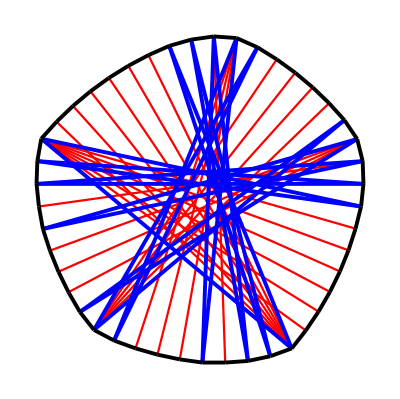

```mathematica
dcrp[{1 ,1 ,1 ,7 ,7 ,1 ,1 ,1 ,1 ,2 ,1 ,4 ,1 ,1 ,5 ,1 ,1 ,4 ,1 ,2 ,1}]
```

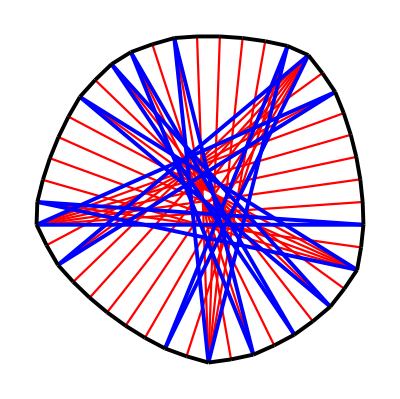

```mathematica
dcrp[{1 ,2 ,5 ,2 ,2 ,2 ,1 ,2 ,2 ,2 ,5 ,2 ,1 ,6 ,2 ,2 ,6}]
```

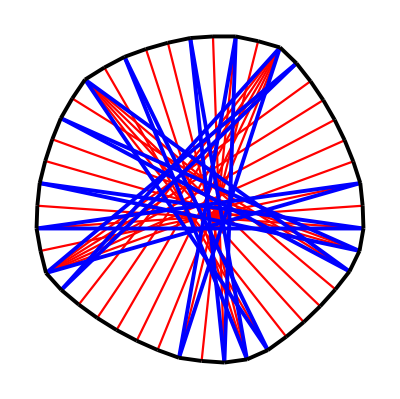

```mathematica
dcrp[{2 ,1 ,3 ,1 ,2 ,5 ,2 ,1 ,3 ,1 ,2 ,2 ,2 ,6 ,1 ,1 ,6 ,2 ,2}]
```

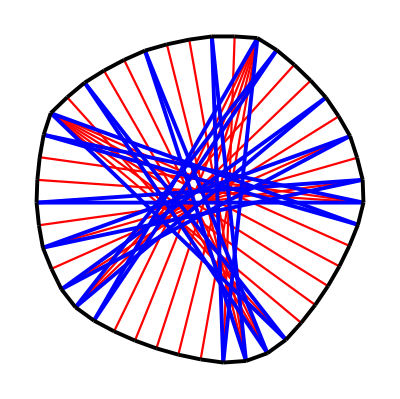

```mathematica
dcrp[{3 ,1 ,1 ,6 ,2 ,1 ,3 ,1 ,3 ,1 ,2 ,6 ,1 ,1 ,3 ,1 ,2 ,2 ,2 ,2 ,1}]
```

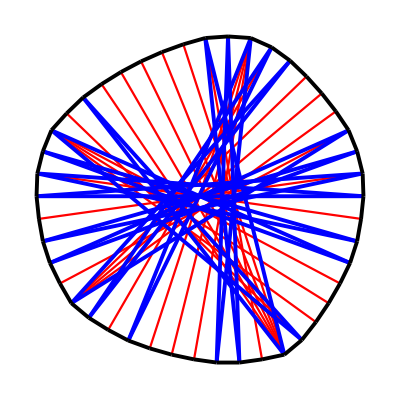

```mathematica
dcrp[{1 ,2 ,1 ,1 ,1 ,4 ,2 ,1 ,6 ,2 ,1 ,1 ,1 ,4 ,1 ,2 ,1 ,1 ,4 ,2 ,1 ,1 ,1 ,2 ,1}]
```

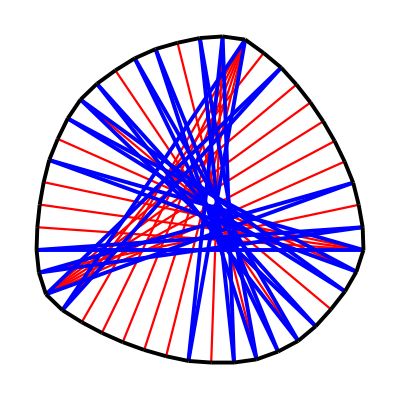

```mathematica
dcrp[{4 ,1 ,2 ,1 ,1 ,2 ,1 ,1 ,2 ,1 ,1 ,1 ,2 ,1 ,1 ,2 ,1 ,6 ,2 ,1 ,6 ,1 ,2 ,1,1}]
```

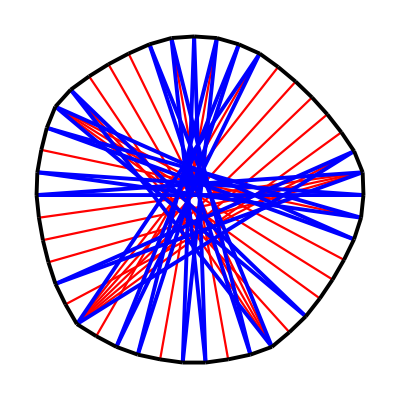

```mathematica
dcrp[{1 ,1 ,2 ,1 ,1 ,4 ,1 ,2 ,4 ,1 ,1 ,2 ,1 ,1 ,1 ,2 ,1 ,1 ,1 ,2 ,6 ,2 ,1 ,4 ,1}]
```

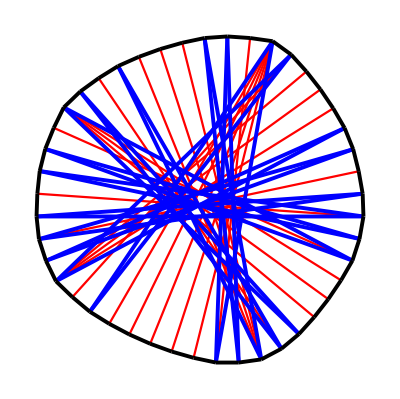

```mathematica
dcrp[{2 ,1 ,1 ,1 ,2 ,4 ,1 ,1 ,2 ,1 ,4 ,1 ,1 ,1 ,2 ,6 ,1, 2, 4 ,1 ,1 ,1 ,2 ,1,1}]
```

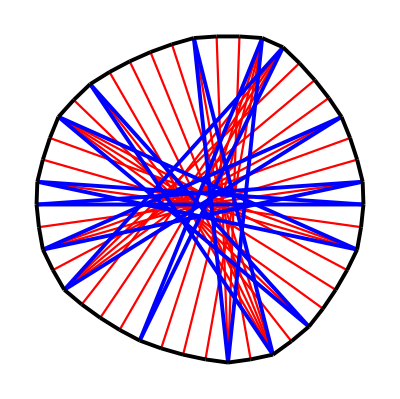

```mathematica
dcrp[{1, 2, 3 ,4 ,2 ,2 ,5 ,2 ,3 ,4 ,1 ,4 ,4 ,2 ,3 ,2 ,1}]
```

```mathematica
dcrp[{'11','2','1','6','1','2','1','2','2','2','2','1','2','1','6','1','2'}]
```

```mathematica
Total[{11,2,1,6,1,2,1,2,2,2,2,1,2,1,6,1,2}]
```

45

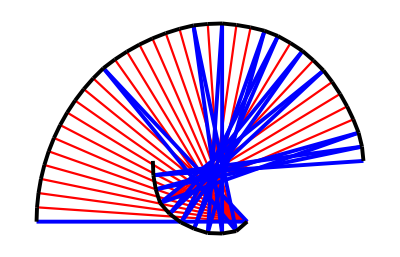

```mathematica
dcrp[{12 ,1 ,7 ,1 ,2 ,1 ,3 ,1 ,1 ,1 ,2 ,1 ,2 ,1 ,5 ,1 ,1 ,1 ,1,1}]
```

```mathematica
Total[{10 ,10 ,1 ,2 ,1 ,1 ,4 ,1 ,2 ,1 ,2 ,1 ,4 ,1 ,1 ,2 ,1}]
```

45

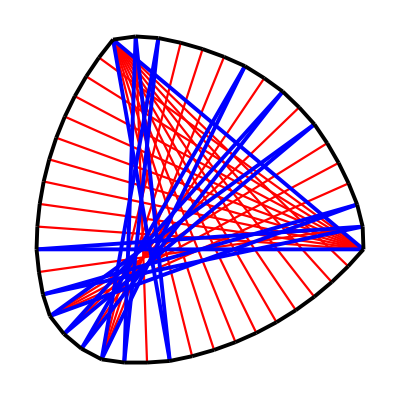

```mathematica
dcrp[{10 ,10 ,1 ,2 ,1 ,1 ,4 ,1 ,2 ,1 ,2 ,1 ,4 ,1 ,1 ,2 ,1}]
```

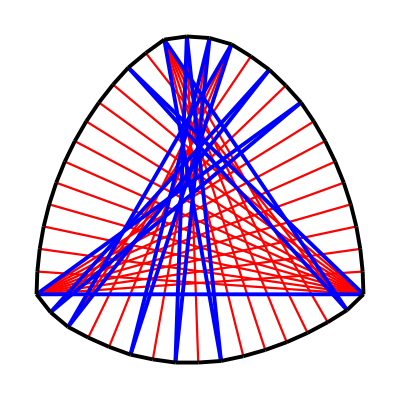

```mathematica
dcrp[{11 ,1 ,2 ,6 ,1 ,2 ,1 ,2 ,1 ,3 ,2 ,1 ,2 ,1 ,9 }]
```

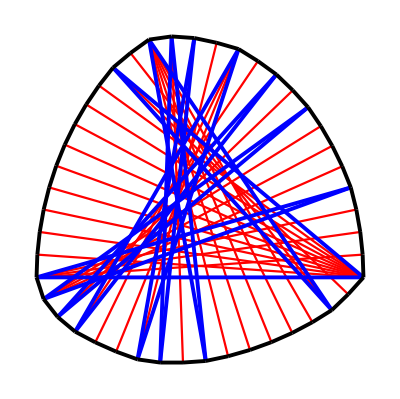

```mathematica
dcrp[{10, 2, 2, 6, 1, 2 ,1 ,1 ,2 ,3 ,2 ,1 ,2 ,1 ,4 ,1 ,4 }]
```

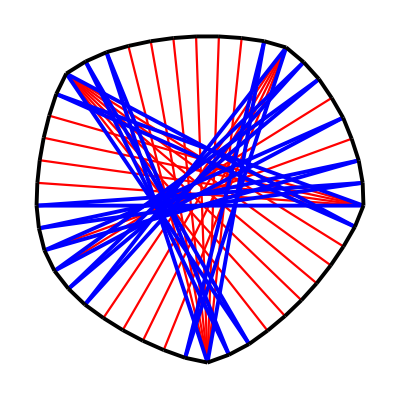

```mathematica
dcrp[{5 ,1 ,1 ,7, 1, 1 ,1 ,1 ,7 ,1 ,1 ,5 ,1 ,1 ,1 ,1 ,2 ,1 ,2 ,1 ,1 ,1,1}]
```

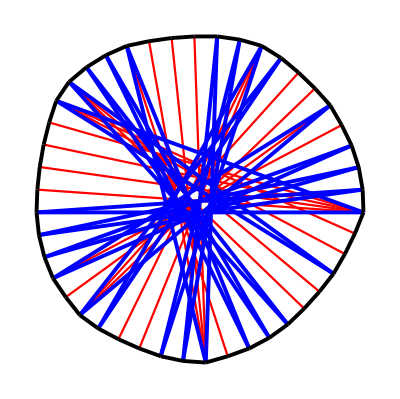

```mathematica
dcrp[{5, 3, 1, 3 ,1 ,1 ,1 ,1 ,1 ,2 ,4 ,1 ,1 ,1 ,1 ,3 ,1 ,1 ,3 ,2 ,2 ,1, 1, 1, 1 ,1 ,1}]
```

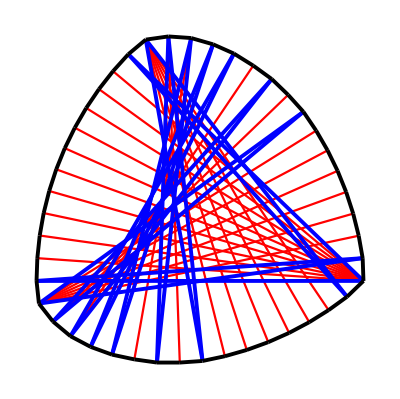

```mathematica
dcrp[{11 ,1 ,1 ,7 ,1 ,2 ,1 ,2, 1, 1 ,1 ,1 ,2 ,1 ,2 ,1 ,7 ,1 ,1}]
```

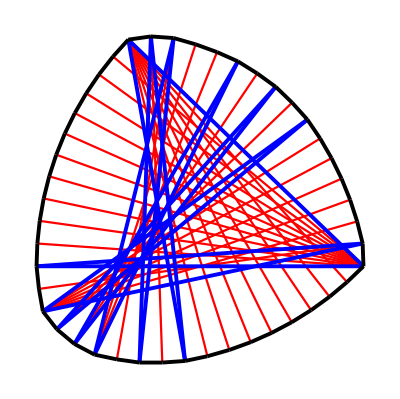

```mathematica
dcrp[{11, 9 ,1 ,2 ,1 ,2 ,3 ,1 ,2 ,1 ,2 ,1 ,6 ,2 ,1}]
```

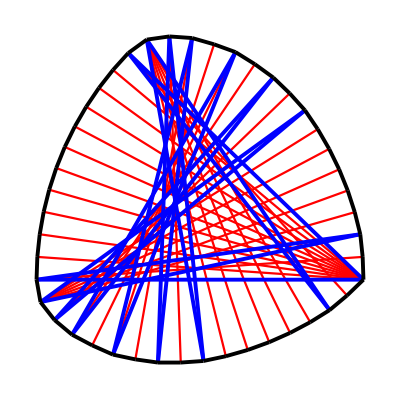

```mathematica
dcrp[{11, 2 ,1 ,6 ,1 ,2 ,1 ,2 ,2 ,2 ,2 ,1 ,2 ,1 ,6 ,1 ,2}]
```

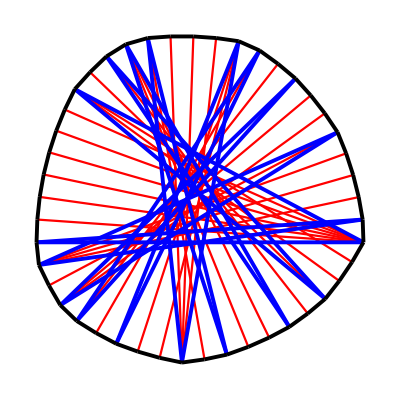

```mathematica
dcrp[{7, 3 ,2 ,2 ,1 ,3 ,1 ,2 ,4 ,3 ,1 ,2 ,2 ,1 ,3 ,2 ,4 ,1 ,1}]
```

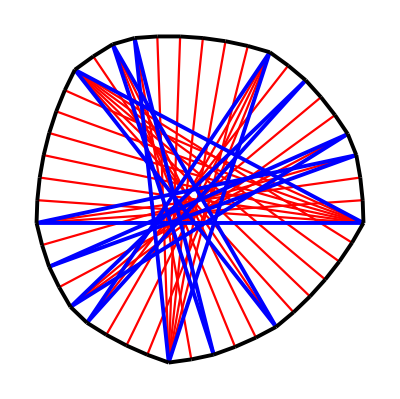

```mathematica
dcrp[{7,6,2,3,1,2,6,4,2,1,3,2,1,2,3}]
```

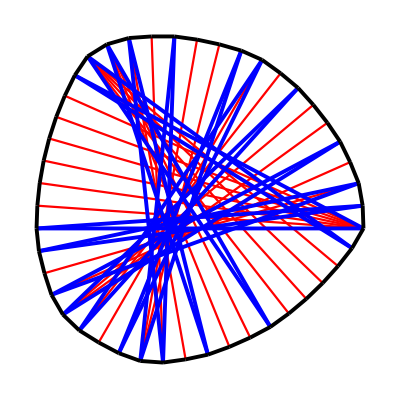

```mathematica
dcrp[{7 ,1 ,1, 5, 1, 3 ,1 ,2 ,2 ,1 ,3 ,1 ,1 ,2 ,2 ,1 ,3 ,1 ,2 ,2 ,1 ,1 ,1}]
```

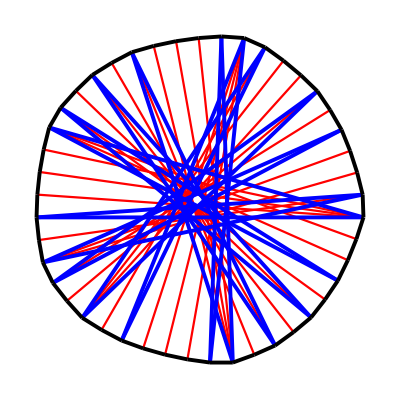

```mathematica
dcrp[{4 ,3 ,1 ,2 ,2 ,2 ,2 ,2 ,4 ,1 ,1 ,4 ,1 ,2, 3, 2 ,2 ,1 ,3 ,2 ,1}]
```

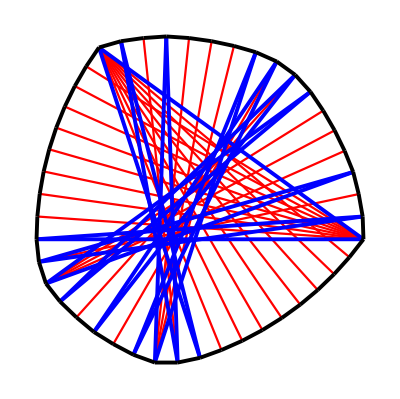

```mathematica
dcrp[{9,9,1,1,2,1,4,1,1,2,1,2,1,1,4,1,2,1,1}]
```

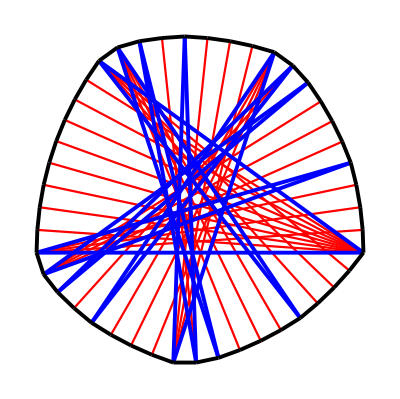

```mathematica
dcrp[{9,4,1,4,1,1,2,1,4,4,1,2,1,1,4,1,4}]
```

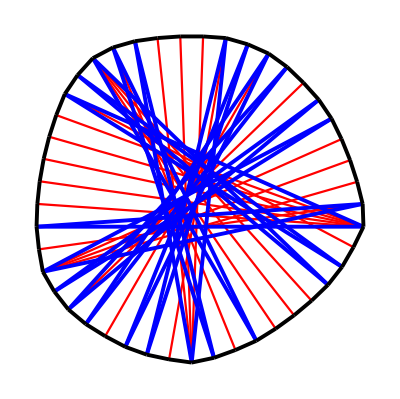

```mathematica
dcrp[{6, 2, 1, 1, 1, 4, 1, 2, 1, 1, 4, 2, 1, 1, 1, 2, 1, 1, 2, 1, 1, 1, 4, 2, 1}]
```

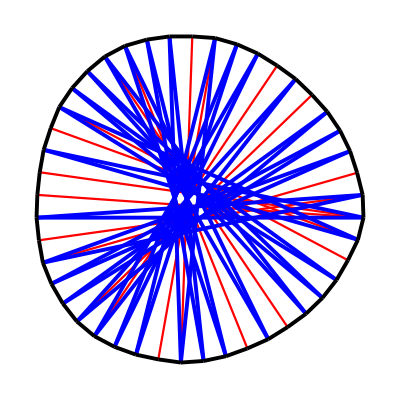

```mathematica
dcrp[{3,1,2,2,1,1,1,1,1,2,1,2,1,1,1,1,2,2,1,1,1,1,2,1,2,1,1,1,1,1,2,2,1}]
```

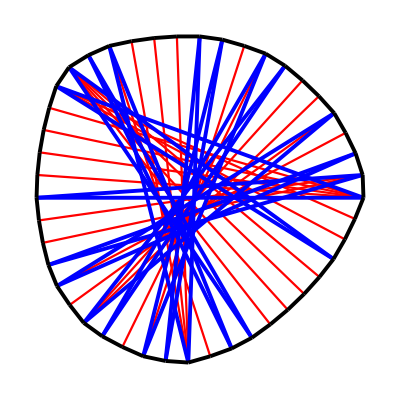

```mathematica
dcrp[{5,3,1,5,1,1,1,2,4,1,1,1,2,2,1,1,3,2,2,1,1,3,1}]
```

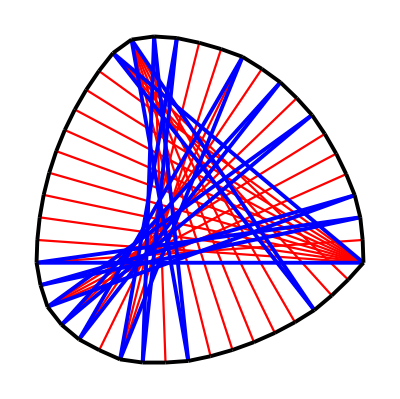

```mathematica
dcrp[{10 ,3 ,1 ,6 ,1 ,2 ,1 ,1 ,3 ,2 ,2 ,1 ,2 ,1 ,4 ,1 ,1 ,1 ,2}]
```

```mathematica
dcrp[{10,10,1,2,1,1,4,1,2,1,2,1,4,1,1,2,1}]
```

-Graphics-

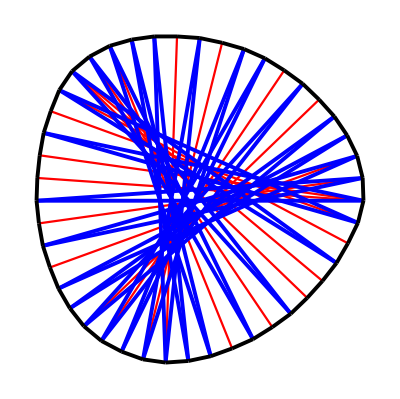

```mathematica
dcrp[{3, 1, 2, 2, 1, 3, 1, 2, 1, 2, 1, 1, 1, 1, 2, 1, 2, 1, 1, 1, 2, 1, 2,1, 1, 1, 1, 2, 1, 2, 1}]
```

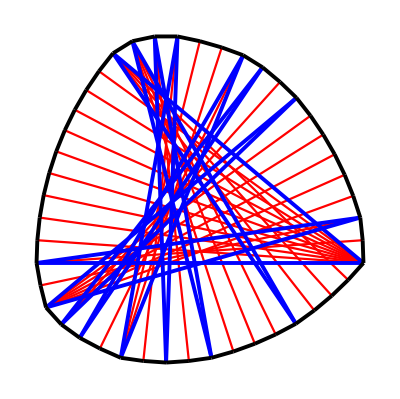

```mathematica
dcrp[{10,4,1,4,1,2,1,2,3,2,1,1,2,1,6,2,2}]
```

```mathematica
dcrp[{9,5,1,3,2,1,2,1,3,5,1,2,6,1,3}]
```

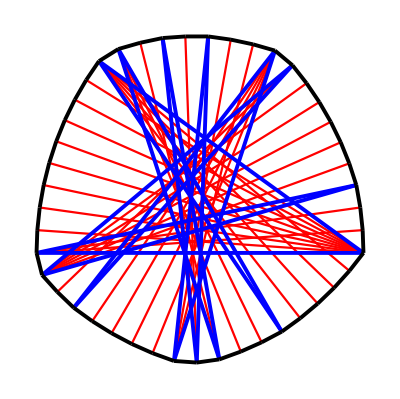

```mathematica
dcrp[{11,9,1,2,1,2,3,1,2,1,2,1,6,2,1}]
```

-Graphics-

```mathematica
dcrp[{11,2,1,6,1,2,1,2,2,2,2,1,2,1,6,1,2}]
```

-Graphics-